```mathematica
Off[RowReduce::luc]
Off[Solve::svars]
$Assumptions={θ>0,n∈Integers,m∈Integers,j∈Integers,i∈Integers,n≥0,m≥0,j≥0,i≥0};
SetOptions[Plot,
PlotStyle->{{Red,Thick},{Purple,Thick},{Blue,Thick},{Cyan,Thick}},
Frame->True,
BaseStyle->{Medium,FontFamily->"Helvetica"},
ImageSize->600];

colorlist={Blue,Red,Darker[Green],Darker[Yellow],Orange,Lighter[Green],Lighter[Brown],Purple,Cyan}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

## Some Testing with Hermite Functions (non-normalized)

```mathematica
f0[c_]=1/(√(2π))Exp[-c^2/2];
fM[c_]=(v)f0[c];
H[i_,c_]=1/(i!2^(i/2))HermiteH[i,c/√2];
fG[c_,n_]:=∑_(k=0)^(n-1) α[k]H[k,c]f0[c];
```

```mathematica
HSpcInt[n_,m_]:=Which[m==n,1/(2n!),OddQ[m-n],1/(√(2 π))1/(n!)(∑_(i=1)^n (2^(1/2 (1-2 i+m+n)) π)/(Gamma[(i-m)/2] Gamma[2-i+m] Gamma[1/2 (1+i-n)])+((m-n-2)!!(-1)^((m-n-1)/2))/((m-n)!)),EvenQ[m-n],0];
```

```mathematica
Table[NIntegrate[k!H[k,c]^2 f0[c],{c,-Infinity,Infinity}],{k,0,10}]
Table[Expand[(i+1)H[i+1,c]-(c H[i,c]- H[i-1,c])],{i,1,10}]
FullSimplify[D[H[i,c],c]-H[i-1,c]]
FullSimplify[D[H[i,c]f0[c],c]+(i+1)H[i+1,c]f0[c]]
(*Table[n!(NIntegrate[H[n,c](fM[c]-fG[c,5]),{c,-Infinity,Infinity}]),{n,0,4}]/.{α[0]->v}*)
```

{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}

{0,0,0,0,0,0,0,0,0,0}

0

0

```mathematica
∫_(-∞)^∞ H[1,c]fG[c,5]ⅆc
```

$Aborted

```mathematica
Expand[H[1,c]]
```

c

```mathematica
Table[HSpcInt[n,m],{n,0,3},{m,0,5}]
Table[∫_0^∞ H[n,c]H[m,c]f0[c]ⅆc,{n,0,3},{m,0,5}]
```

{{1/2,1/(√(2 π)),0,-1/(6 √(2 π)),0,1/(40 √(2 π))},{1/(√(2 π)),1/2,1/(2 √(2 π)),0,-1/(24 √(2 π)),0},{0,1/(2 √(2 π)),1/4,1/(4 √(2 π)),0,-1/(48 √(2 π))},{-1/(6 √(2 π)),0,1/(4 √(2 π)),1/12,1/(16 √(2 π)),0}}

{{1/2,1/(√(2 π)),0,-1/(6 √(2 π)),0,1/(40 √(2 π))},{1/(√(2 π)),1/2,1/(2 √(2 π)),0,-1/(24 √(2 π)),0},{0,1/(2 √(2 π)),1/4,1/(4 √(2 π)),0,-1/(48 √(2 π))},{-1/(6 √(2 π)),0,1/(4 √(2 π)),1/12,1/(16 √(2 π)),0}}

## Some Testing with Hermite Functions (normalized)

```mathematica
f0[c_]=1/(√(2π))Exp[-c^2/2];
fM[c_]=(c v-θ/2+(c^2 θ)/2+ρ)f0[c];
H[i_,c_]=1/(√Gamma[i+1] 2^(i/2))HermiteH[i,c/√2];
fG[c_,n_]:=∑_(k=0)^(n-1) α[k]H[k,c]f0[c];

(*The following routine integrates the following expressions ∫_0^∞ H[n,c]H[m,c]f0[c]ⅆc *)
```

```mathematica
HSpcInt[n_,m_]:=Which[m==n,1/2,OddQ[m-n],1/(√(2 π))(√(n!m!))/(n!)(∑_(i=1)^n (2^(1/2 (1-2 i+m+n)) π)/(Gamma[(i-m)/2] Gamma[2-i+m] Gamma[1/2 (1+i-n)])+((m-n-2)!!(-1)^((m-n-1)/2))/((m-n)!)),EvenQ[m-n],0];
```

```mathematica
Table[∫_(-∞)^∞ H[k,c]^2 f0[c]ⅆc,{k,0,4}]
Table[Expand[√(i+1)H[i+1,c]-(c H[i,c]- √i H[i-1,c])],{i,1,10}]
FullSimplify[D[H[i,c],c]-√i H[i-1,c]]
FullSimplify[D[H[i,c]f0[c],c]+√(i+1)H[i+1,c]f0[c]]
Table[(∫_(-∞)^∞ (c)^n fG[c,4]ⅆc),{n,0,4}]
Table[(∫_(-∞)^∞ H[n,c](fM[c]-fG[c,5])ⅆc),{n,0,4}]/.{α[0]->ρ,α[1]->v,α[2]->θ/√2}
```

{1,1,1,1,1}

{0,0,0,√(2/3) c^3+√(3/2) c^3-(5 c^3)/(√6),0,0,0,0,0,0}

(2^(1/2-i/2) √i (√i √Gamma[i]-√Gamma[1+i]) HermiteH[-1+i,c/(√2)])/(√Gamma[i] √Gamma[1+i])

(2^(-1-i/2) ⅇ^(-c^2/2) (√Gamma[2+i] (2 i HermiteH[-1+i,c/(√2)]-√2 c HermiteH[i,c/(√2)])+√(1+i) √Gamma[1+i] HermiteH[1+i,c/(√2)]))/(√π √Gamma[1+i] √Gamma[2+i])

$Aborted

$Aborted

```mathematica
∫_(-∞)^∞ (c)^2 fM[c]ⅆc
```

θ+ρ

```mathematica
Expand[H[2,c]]
```

-1/(√2)+c^2/(√2)

```mathematica
Expand[√6 H[3,c]]
```

-3 c+c^3

```mathematica
Table[HSpcInt[n,m],{n,0,3},{m,0,5}]
Table[∫_0^∞ H[n,c]H[m,c]f0[c]ⅆc,{n,0,3},{m,0,5}]
```

{{1/2,1/(√(2 π)),0,-1/(2 √(3 π)),0,1/4 √(3/(5 π))},{1/(√(2 π)),1/2,1/(2 √π),0,-1/(4 √(3 π)),0},{0,1/(2 √π),1/2,1/2 √(3/(2 π)),0,-1/4 √(5/(6 π))},{-1/(2 √(3 π)),0,1/2 √(3/(2 π)),1/2,3/(4 √(2 π)),0}}

{{1/2,1/(√(2 π)),0,-1/(2 √(3 π)),0,1/4 √(3/(5 π))},{1/(√(2 π)),1/2,1/(2 √π),0,-1/(4 √(3 π)),0},{0,1/(2 √π),1/2,1/2 √(3/(2 π)),0,-1/4 √(5/(6 π))},{-1/(2 √(3 π)),0,1/2 √(3/(2 π)),1/2,3/(4 √(2 π)),0}}

## Equations for α_j, incl. Eigenvalues

(0 | 1 | 0 | 0
1 | 0 | √2 | 0
0 | √2 | 0 | √3
0 | 0 | √3 | 0)

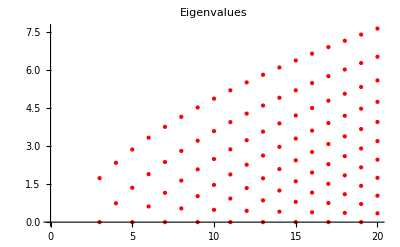

```mathematica
AA[n_]:=Table[If[i==j+1,√i,If[i==j-1,√(i+1),0]],{i,0,n-1},{j,0,n-1}]

MatrixForm[AA[4]]
ListPlot[N[Table[Thread[{Table[n,{i,1,If[OddQ[n],(n)/2+1,(n)/2]}],N[Select[Eigenvalues[AA[n]],#≥0&]]}],{n,3,20}]],PlotLabel->"Eigenvalues",PlotStyle->{{Red,Thick,PointSize[Large]}}]
```

## Check Boundary Stability

```mathematica
Clear[MatBoe]
```

```mathematica
(*construct Aoe*)
MatAoe[n_]:=Module[{result,numOdd,numEven,IDOdd,IDEven},
IDOdd = If[EvenQ[n],Range[1,n-1,2],Range[1,n-2,2]];
IDEven = If[EvenQ[n],Range[0,n-2,2],Range[0,n-1,2]];

result=ConstantArray[0,{Length[IDOdd],Length[IDEven]}];
Do[Do[If[ii==jj,result⟦ii,jj⟧=Sqrt[IDOdd⟦ii⟧],If[jj==ii+1,result⟦ii,jj⟧=Sqrt[IDOdd⟦ii⟧+1]]],{jj,1,Length[IDEven]}],{ii,1,Length[IDOdd]}];

result

]

(*With the assumption that the normal points from the gas into the wall.*)
MatBoe[n_]:=Module[{result,numOdd,numEven,IDOdd,IDEven,rhoW},
IDOdd = If[EvenQ[n],Range[1,n-1,2],Range[1,n-2,2]];
IDEven = If[EvenQ[n],Range[0,n-2,2],Range[0,n-1,2]];

result=Flatten[ConstantArray[0,{Length[IDOdd],1}]];


(*First we compute the density at the wall*)
rhoW=Expand[ρW/.Solve[(Expand[(ρW HSpcInt[1,0]+0 HSpcInt[1,1]+θW/√2 HSpcInt[1,2])-∑_(j=0)^((n-1)/2) α[2j]HSpcInt[1,2j]])==0,ρW]⟦1⟧];


(*2 comes from the left hand side of the boundary conditions*)
Do[result⟦ii⟧=-2((rhoW HSpcInt[IDOdd⟦ii⟧,0]+0 HSpcInt[IDOdd⟦ii⟧,1]+θW/√2 HSpcInt[IDOdd⟦ii⟧,2])-∑_(j=0)^((n-1)/2) α[2j]HSpcInt[IDOdd⟦ii⟧,2j]),{ii,1,Length[IDOdd]}];

CoefficientArrays[result,Map[α[#]&,IDEven]]⟦2⟧
]

MatOnsager[n_]:=Module[{Btilde,result},

Btilde=MatBoe[n]⟦1;;-1,1;;Length[MatBoe[n]]⟧;
Btilde.Inverse[MatAoe[n]⟦1;;-1,1;;Length[MatAoe[n]]⟧]
]

CheckBoundary[n_]:=Module[{entropy,error,numEntries,OnsagerMat},

OnsagerMat =MatOnsager[n];
error =Simplify[ OnsagerMat-Transpose[OnsagerMat]];
numEntries=Length[Flatten[OnsagerMat]];

Print[Style["Num Tensors: ",FontColor->Black],n];
Print[Style["Checking Symmetricity",FontColor->Magenta]];
If[Count[Flatten[error],0]==numEntries,Print[Style["Symmetric",FontColor->Green]],Print[Style["UnSymmetric",FontColor->Red]]];

Print[Style["Checking Eigenvalues",FontColor->Brown]];
If[Length[Select[Eigenvalues[OnsagerMat],#<0&]]>0,Print[Style["Negative Definite",FontColor->Red]],Print[Style["Positive Definite",FontColor->Green]]];

]

(*Explicit Formulae for Boe^T Aoe*)
ExplicitEntropyNoNullSpace[n_]:=Module[{result,IDOdd,IDEven},

IDOdd = If[EvenQ[n],Range[1,n-1,2],Range[1,n-2,2]];
IDEven = If[EvenQ[n],Range[0,n-2,2],Range[0,n-1,2]];
result=ConstantArray[0,{Length[IDEven],Length[IDEven]}];

Do[Do[result⟦ii,jj⟧=2*(HSpcInt[2 ii -2,2 jj-1] √(2 jj-1)+If[jj>1,HSpcInt[2 ii -2,2 jj -3] √(2 jj -2),0]);,{jj,1,Length[IDEven]}];,{ii,1,Length[IDOdd]}];

result
]
```

### Stability Check

```mathematica
oddNtensors = Range[4,20,1];
Do[CheckBoundary[ii],{ii,oddNtensors}];
```

Num Tensors: 4

Checking Symmetricity

Symmetric

Checking Eigenvalues

Positive Definite

Num Tensors: 5

Checking Symmetricity

Symmetric

Checking Eigenvalues

Positive Definite

Num Tensors: 6

Checking Symmetricity

Symmetric

Checking Eigenvalues

Positive Definite

Num Tensors: 7

Checking Symmetricity

Symmetric

Checking Eigenvalues

Positive Definite

Num Tensors: 8

Checking Symmetricity

Symmetric

Checking Eigenvalues

Positive Definite

Num Tensors: 9

Checking Symmetricity

Symmetric

Checking Eigenvalues

Positive Definite

Num Tensors: 10

Checking Symmetricity

Symmetric

Checking Eigenvalues

Positive Definite

Num Tensors: 11

Checking Symmetricity

Symmetric

Checking Eigenvalues

Positive Definite

Num Tensors: 12

Checking Symmetricity

Symmetric

Checking Eigenvalues

Positive Definite

Num Tensors: 13

Checking Symmetricity

Symmetric

Checking Eigenvalues

Positive Definite

Num Tensors: 14

Checking Symmetricity

Symmetric

Checking Eigenvalues

Positive Definite

Num Tensors: 15

Checking Symmetricity

Symmetric

Checking Eigenvalues

Positive Definite

Num Tensors: 16

Checking Symmetricity

Symmetric

Checking Eigenvalues

Positive Definite

Num Tensors: 17

Checking Symmetricity

Symmetric

Checking Eigenvalues

Positive Definite

Num Tensors: 18

Checking Symmetricity

Symmetric

Checking Eigenvalues

Positive Definite

Num Tensors: 19

Checking Symmetricity

Symmetric

Checking Eigenvalues

Positive Definite

Num Tensors: 20

Checking Symmetricity

Symmetric

Checking Eigenvalues

Positive Definite

## Construct Stable Boundary Conditions

```mathematica
(*flag == 0 for unstable,flag == 1 for stable*)
ConstructStableBC[n_,flag_]:=Module[{BCMat,OddVar,EvenVar,IDEven,IDOdd,result,Boe},


IDOdd = If[EvenQ[n],Range[1,n-1,2],Range[1,n-2,2]];
IDEven = If[EvenQ[n],Range[0,n-2,2],Range[0,n-1,2]];
result=Flatten[ConstantArray[0,{Length[IDOdd]-1}]];

OddVar=Map[α[#]&,IDOdd];
EvenVar=Map[α[#]&,IDEven];

If[flag==0,Boe = MatBoe[n],Boe=MatOnsager[n].MatAoe[n]];

(*we neglect the first boundary condition*)
Do[result⟦ii⟧=α[IDOdd⟦ii+1⟧]-Boe⟦ii+1,All⟧.Map[α[#]&,IDEven]+Boe⟦ii+1,2⟧/(√2)θW,{ii,1,Length[IDOdd]-1}];

Expand[Simplify[result]]
]
```

```mathematica
MBC=ConstructStableBC[9,0];
PBC=ConstructStableBC[9,1];
Table[Simplify[(bc0⟦ii⟧/β1/.{β1->√(π/2)1/2})-PBC⟦ii⟧],{ii,1,Length[MBC]}]
```

{0,0,0}

```mathematica
AA[5]//MatrixForm
```

AA[5]

## Solving

```mathematica
Clear[nvar,kn,thetaw,A0,P0,λ0,λ,λPlus,v,vv,B0,alpha,coef,Kn,k,Ansatz,Coefs,SymmetryConditions,solution,res,bcEqn,solBC]

(*flag = 0 for unstable, flag == 1 for stable*)
GetSolution[nvar_,kn_,thetaw_,flag_]:=Block[{λ0,λ,λPlus,v,vv,B0,alpha,coef,Kn,vW,k,Ansatz,Coefs,SymmetryConditions,solution,res,bcEqn,solBC,bc0},
A0=AA[nvar];
P0=SparseArray[{{i_,i_}->-1},nvar];
P0⟦1,1⟧=0;
P0⟦2,2⟧=0;
P0⟦3,3⟧=0;

{λ0,vv}=Eigensystem[{P0,1.0A0}];
λ=Select[λ0,(0<Abs[#]<∞)&];
v=Extract[vv,Flatten[Table[Position[λ0,item],{item,λ}],1]];

λ=Flatten[Table[{Rationalize[λ⟦ii⟧,0],-Rationalize[λ⟦ii⟧,0]},{ii,1,Length[λ],2}]];
λPlus=Select[λ,(#>0)&];

B0=Table[0,{i,1,nvar}];
B0⟦1⟧=0;
alpha=0;

coef[0,4]=Kn k[0]; (* heat flux constant*)
Ansatz[x_]=Table[Sum[coef[jj,ii] x^jj,{jj,0,1}],{ii,1,nvar}];
Coefs=Cases[Flatten[Table[Table[coef[jj,ii],{jj,0,1}],{ii,1,nvar}]],coef[_,_]];

Ansatz[x_]=Ansatz[x]/.Solve[Thread[Flatten[CoefficientList[A0.Ansatz'[x]-1/Kn P0.Ansatz[x]+alpha B0 x^2,x]]==0],Coefs]⟦1⟧/.{coef[_,_]->0};

SymmetryConditions=Table[0,{ii,1,Length[λ],2}];
Do[jj=1;While[v⟦ii,jj⟧==0,jj++];SymmetryConditions⟦(ii+1)/2⟧=(k[ii]->(-Sign[v⟦ii+1,jj⟧/v⟦ii,jj⟧])k[ii+1]),{ii,1,Length[λ],2}];

solution=ExpToTrig[C0 B0+Ansatz[x]+Sum[k[ii] v⟦ii⟧Exp[λ⟦ii⟧x/Kn],{ii,1,Length[λ]}]/.SymmetryConditions/.Table[k[ii]->k[ii/2],{ii,1,Length[λ]}]];
res=Thread[Table[α[i],{i,0,nvar-1}]->solution/.Table[k[ii]->k[ii]Exp[-λPlus⟦ii⟧(1/2)/Kn],{ii,1,Length[λPlus]}]];


If[flag==0,bc0=ConstructStableBC[nvar,0],bc0=ConstructStableBC[nvar,1]];

bcEqn=Table[bc0⟦i⟧,{i,1,nvar/2-1}]/.res/.{x->1/2}/.{β1->√(π/2)(2-χ)/(2χ)}/.{χ->1};

solBC=Solve[Thread[(bcEqn/.{Kn->kn,θW->thetaw})==0],Table[k[i],{i,0,nvar/2-2}]]⟦1⟧;

(*Table[α[i],{i,0,nvar-1}]/.res/.solBC/.{Kn->kn}*)
{{√2. α[2],√6. α[3]}/.res/.solBC/.{Kn->kn},Table[α[i],{i,0,nvar-1}]/.res/.solBC/.{Kn->kn}}
]
```

```mathematica
(*u[x_]=GetSolution[4,0.1,1.0]
Chop[Expand[N[A0.u'[x]-1/Kn P0.u[x]]/.{Kn->0.1}]]
*)
```

```mathematica
Expand[GetSolution[5,0.1,1.0,1]]
```

{1.45349 x,-0.436048}

{1.45349 x,-0.436048}

## Solution Convergence

### convergence of jump at the wall

```mathematica
Solution[1]=Table[GetSolution[n,0.1,1.0,0]⟦1⟧,{n,5,11}];
SolutionNew[1]=Table[GetSolution[n,0.1,1.0,1]⟦1⟧,{n,5,11}];
```

```mathematica
Do[
TempW[k]=Table[{4+i,1-(Solution[k]⟦i,1⟧/.{x->0.4})},{i,1,Length[Solution[k]]}];
,{k,1,1}]

Do[
TempWNew[k]=Table[{4+i,1-SolutionNew[k]⟦i,1⟧/.{x->0.4}},{i,1,Length[Solution[k]]}];
,{k,1,1}]
```

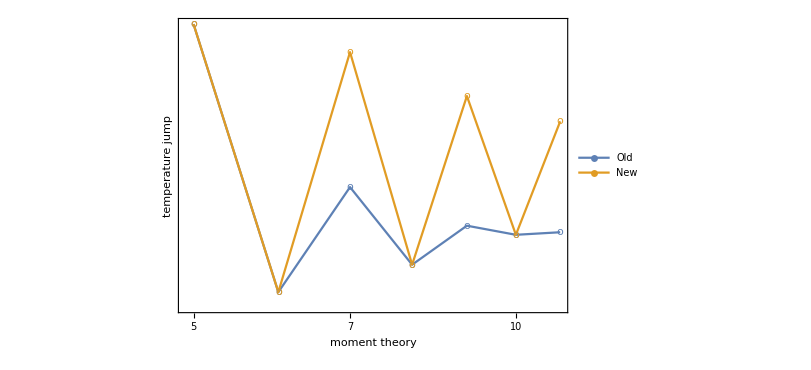

```mathematica
ListLogLogPlot[{TempW[1],TempWNew[1]},Joined->True,Frame->True,PlotRange->{All,Full},BaseStyle->{Medium,FontFamily->"Helvetia"},FrameLabel->{"moment theory","temperature jump","1D Kinetic Equation: Kn = 0.1"},PlotMarkers->{"o"},ImageSize->600,PlotLegends->{"Old","New"}]
```

## Variation of Phase Density Function